```mathematica
Clear[ω, A, g]
```

```mathematica
D[(2*g*A*Sin[ω t])^(1/2),t]
```

(A g ω Cos[t ω])/(√2 √(A g Sin[t ω]))

```mathematica
Funct=%;
```

```mathematica
Reduce[Funct== 0, t]
```

(C[1]∈ℤ&&ω≠0&&(t==(-π/2+2 π C[1])/ω||t==(π/2+2 π C[1])/ω))||A==0||g==0||ω==0

```mathematica
ω = 0.5;
A = .75;
g = 9.8;
```

```mathematica
Funct2 = Funct
```

(0.958514 Cos[0.5 t])/(√Sin[0.5 t])

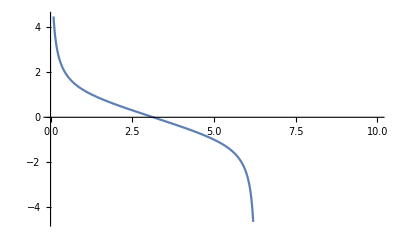

```mathematica
Plot[Funct2,{t,0,10}]
```

```mathematica
sinfunc = (20Sin[ω t])^(3/2)
```

40 √5 Sin[0.5 t]^(3/2)

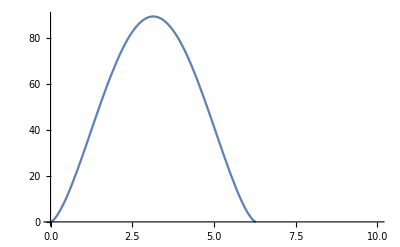

```mathematica
Plot[sinfunc,{t,0,10}]
```

```mathematica
abssinfunc = Abs[sinfunc]
```

40 √5 Abs[Sin[0.5 t]]^(3/2)

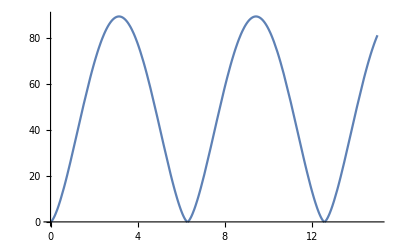

```mathematica
Plot[abssinfunc,{t,0,15}]
```

```mathematica
wveloc = √(2*g*abssinfunc);
```

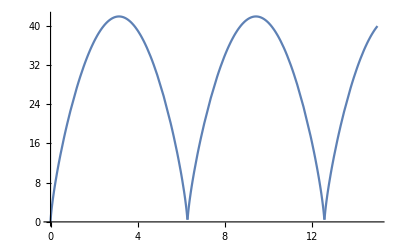

```mathematica
Plot[wveloc,{t,0,15}]
```